# analytics

## derive eoms

## de Turk eoms

### definitions

```mathematica
<<EDCRGTCcode.m;
xIN={z,t,x,y};

ds2 =1/z^2( - (1-z) P[z]Qtt[x,z] dt^2 + (Qzz[x,z] dz^2)/(P[z](1-z)) + Qxx[x,z](dx + z^2 Qxz[x,z] dz)^2 + Qyy[x,z] dy^2);
repscoords = {dz-> dx[1],dt-> dx[2],dx-> dx[3],dy-> dx[4]};

ds2aux = Simplify[ds2 /. repscoords];
g=Table[1/2 D[D[ds2aux, dx[j]], dx[i]], {i,1,4},  {j,1,4} ];
simpRules=TrigRules;

RGtensors[g,xIN,{1,0,0}];
```

gdd = ((2 z^4 Qxx[x,z] Qxz[x,z]^2+(2 Qzz[x,z])/(P[z]-z P[z]))/(2 z^2) | 0 | Qxx[x,z] Qxz[x,z] | 0
0 | ((-1+z) P[z] Qtt[x,z])/z^2 | 0 | 0
Qxx[x,z] Qxz[x,z] | 0 | Qxx[x,z]/z^2 | 0
0 | 0 | 0 | Qyy[x,z]/z^2)

LineElement = ((-1+z) d[t]^2 P[z] Qtt[x,z])/z^2+(d[x]^2 Qxx[x,z])/z^2+2 d[x] d[z] Qxx[x,z] Qxz[x,z]+(d[y]^2 Qyy[x,z])/z^2+(d[z]^2 (-z^4 P[z] Qxx[x,z] Qxz[x,z]^2+z^5 P[z] Qxx[x,z] Qxz[x,z]^2-Qzz[x,z]))/((-1+z) z^2 P[z])

gUU = (-((-1+z) z^2 P[z])/Qzz[x,z] | 0 | ((-1+z) z^4 P[z] Qxz[x,z])/Qzz[x,z] | 0
0 | z^2/((-1+z) P[z] Qtt[x,z]) | 0 | 0
((-1+z) z^4 P[z] Qxz[x,z])/Qzz[x,z] | 0 | -(z^2 (-z^4 P[z] Qxx[x,z] Qxz[x,z]^2+z^5 P[z] Qxx[x,z] Qxz[x,z]^2-Qzz[x,z]))/(Qxx[x,z] Qzz[x,z]) | 0
0 | 0 | 0 | z^2/Qyy[x,z])

gUU computed in 0.012065 sec

Gamma computed in 0.051355 sec

Riemann(dddd) computed in 0.502132 sec

Riemann(Uddd) computed in 1.28407 sec

Ricci computed in 2.67463 sec

Weyl tensor not computed

Einstein tensor not computed

All tasks completed in 4.53289 seconds

gauge fields

```mathematica
Ad={0,(1-z) a[x,z],0,0};
AU=Raise[Ad,1];

Fdd=-covD[Ad]+ Transpose[covD[Ad]];
FUU= Raise[Fdd,1,2];
FdU=Raise[Fdd,2];
FUd=Raise[Fdd,1];
F2= multiDot[Fdd,FUU,{1,1},{2,2}];

EU = covDiv[FUU,{2,{1}}] ;

Einsdd=Rdd + 3 gdd -(multiDot[Fdd,FdU,{2,2}] - 1/4 F2 gdd );
```

### check RN solution

```mathematica
solnRN = {Qzz-> Function[{x,z}, 1], Qtt-> Function[{x,z}, 1], Qxx-> Function[{x,z}, 1], Qxz-> Function[{x,z}, 0], Qyy-> Function[{x,z}, 1], a-> Function[{x,z}, μ1 ]};

repP ={P-> Function[z, 1 + z + z^2 - (μ1^2 z^3)/2 ]};
```

```mathematica
Simplify[ {Einsdd , EU} /. solnRN  /. repP  ]
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{0,0,0,0}}

### eins eoms with de Turk

```mathematica
GbarUdd = GUdd /. solnRN;
```

```mathematica
ξU = Contract[ Raise[ GUdd - GbarUdd , 2] , {2,3}];
ξd = Lower[ξU,1] // Simplify;
```

```mathematica
EinsHdd = Einsdd - 1/2(covD[ξd]+ Transpose[covD[ξd]]);
```

```mathematica
ξNorm= Simplify[  multiDot[ξU , ξd, {1,1 } ] /. repP ];
```

### non-trivial equations

variables Qzz, Qtt, Qxz, Qxx, Qyy, a

```mathematica
Position[EinsHdd,x_/;!TrueQ[x==0],{2},Heads->False]
```

{{1,1},{1,3},{2,2},{3,1},{3,3},{4,4}}

```mathematica
Position[EU,x_/;!TrueQ[x==0],{1},Heads->False]
```

{{2}}

### all eqs

```mathematica
SetDirectory["Documents/Physics/teaching/school\ concepcion/nb"];
```

```mathematica
alleqsAUX = {EU[[2]], EinsHdd[[1,1]] , EinsHdd[[1,3]], EinsHdd[[2,2]], EinsHdd[[3,3]], EinsHdd[[4,4]] }// Simplify;
```

```mathematica
EqsRep = Solve[ alleqsAUX  ==0 , D[ {a[x,z],Qtt[x,z],Qzz[x,z],Qxx[x,z], Qyy[x,z], Qxz[x,z]} , z, z ] ][[1]] // Simplify;
```

```mathematica
alleqs = D[ {a[x,z],Qtt[x,z],Qzz[x,z],Qxx[x,z], Qyy[x,z], Qxz[x,z]} , z, z ] - Evaluate[ D[ {a[x,z],Qtt[x,z],Qzz[x,z],Qxx[x,z], Qyy[x,z], Qxz[x,z]} , z, z ] /.  EqsRep  ];
```

### IR asympt

```mathematica
repIR = {Qzz[x,1]-> Qtt[x,1], D[Qzz[x,1]-> Qtt[x,1] , x], D[Qzz[x,1]-> Qtt[x,1] ,x,  x]};
```

```mathematica
eqsIRtemp = Collect[ Series[ u alleqs /. repP  /. z-> 1 - u ,{u,0,0} ]/. repIR  , u, Simplify] /. F_[x,1]-> F[x,y];
```

```mathematica
solveIRbcs = Solve[ eqsIRtemp == 0 , D[ {a[x,y], Qtt[x,y], Qxx[x,y], Qyy[x,y], Qxz[x,y]}  ,y]][[1]]  // Simplify;
```

```mathematica
IRbcs =  {D[ a[x,y], y ], Qzz[x,y] , D[  Qtt[x,y], y],D[  Qxx[x,y], y], D[ Qyy[x,y], y],D[  Qxz[x,y], y ]   } - Evaluate[ { D[ a[x,y], y ] , Qtt[x,y] , D[  Qtt[x,y], y],D[  Qxx[x,y], y], D[ Qyy[x,y], y],D[  Qxz[x,y], y ]    }  /.  solveIRbcs   ];
```

```mathematica
(*Export[ "Setup_HST_DeTurk.m" , {alleqs,ξNorm,IRbcs }];*)
```

```mathematica
{alleqs,ξNorm,IRbcs }= Import[ "Setup_HST_DeTurk.m" ];
```

## numerics

## preliminaries

### import eoms

```mathematica
repP ={P-> Function[z, 1 + z + z^2 - (μ1^2 z^3)/2 ]};
repx = {x-> x1/k};
```

```mathematica
RepFields = 
{      a-> Function[{x,y},  a[k x,y]  ], 
Qtt->   Function[{x,y},  Qtt[k x,y]  ], 
Qzz->   Function[{x,y},  Qzz[k x,y]  ],
Qxx->   Function[{x,y},  Qxx[k x,y]  ] ,
Qyy->   Function[{x,y},  Qyy[k x,y] ],
Qxz->   Function[{x,y},  Qxz[k x,y] ]   };
```

```mathematica
SetDirectory["Documents/Physics/teaching/school\ concepcion/nb"];
{alleqsAUX,ξNormAUX,IRbcs } = Import["Setup_HST_DeTurk.m"] /. z-> y /. repP  /. repx /. RepFields  /. x1-> x  /. k -> k1 μ  /. μ1-> μ; 
Neq = Length[alleqs];
```

```mathematica
alleqs = alleqsAUX // Together // Numerator // Simplify;
```

#### ξNorm

```mathematica
ξNorm= (Qxx[x,y]^2 Qyy[x,y]^2 Qzz[x,y]^2 ((-1+y) y^4 (-2-2 y-2 y^2+y^3 μ^2) (4-2 y^4 μ^2+y^3 (2+μ^2))^2 Qxx[x,y]^2 Qxz[x,y]^2 Qzz[x,y]+4 k1^2 y^2 μ^2 (2+y^4 μ^2-y^3 (2+μ^2)) Qzz[x,y] (Derivative[1,0][Qtt][x,y])^2+2 Qxx[x,y] ((4-2 y^4 μ^2+y^3 (2+μ^2))^2 Qzz[x,y]^2-2 y (-8+2 y^8 μ^4+2 y^3 (2+μ^2)-3 y^7 μ^2 (2+μ^2)+y^6 (2+μ^2)^2) Qzz[x,y] Derivative[0,1][Qtt][x,y]+(-1+y)^2 y^2 (2+2 y+2 y^2-y^3 μ^2)^2 (Derivative[0,1][Qtt][x,y]-k1 y^2 μ Qxz[x,y] Derivative[1,0][Qtt][x,y])^2))-2 Qtt[x,y] Qxx[x,y] Qyy[x,y] Qzz[x,y] (4 k1^2 y^2 μ^2 (2+y^4 μ^2-y^3 (2+μ^2)) Qyy[x,y] Qzz[x,y]^2 Derivative[1,0][Qtt][x,y] Derivative[1,0][Qxx][x,y]+(-1+y) y^4 (8+8 y+8 y^2+2 y^7 μ^4-2 y^3 (-2+μ^2)-2 y^4 (-2+μ^2)-2 y^5 (-2+μ^2)-y^6 μ^2 (6+μ^2)) Qxx[x,y]^3 Qxz[x,y] Qzz[x,y] (y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^3 Qyy[x,y]+2 y (-2-y^4 μ^2+y^3 (2+μ^2)) Qyy[x,y] Derivative[0,1][Qxz][x,y]+Qxz[x,y] (2 (2+y^4 μ^2-y^3 (2+μ^2)) Qzz[x,y]+Qyy[x,y] (-4-6 y^4 μ^2+5 y^3 (2+μ^2)+2 k1 (-1+y) y^3 μ (-2-2 y-2 y^2+y^3 μ^2) Derivative[1,0][Qxz][x,y])))-2 (-1+y) (-2-2 y-2 y^2+y^3 μ^2) Qxx[x,y] Qzz[x,y] (2 k1^2 y^2 μ^2 Qzz[x,y] Derivative[1,0][Qtt][x,y] Derivative[1,0][Qyy][x,y]+Qyy[x,y] ((8-4 y^4 μ^2+2 y^3 (2+μ^2)) Qzz[x,y]^2+y Qzz[x,y] (2 (2+y^4 μ^2-y^3 (2+μ^2)) Derivative[0,1][Qtt][x,y]+(-4+2 y^4 μ^2-y^3 (2+μ^2)) (-Derivative[0,1][Qxx][x,y]+2 k1 y^2 μ Qxz[x,y] Derivative[1,0][Qxx][x,y]))+y^2 ((-1+y) (-2-2 y-2 y^2+y^3 μ^2) Derivative[0,1][Qtt][x,y] (Derivative[0,1][Qxx][x,y]-k1 y^2 μ Qxz[x,y] Derivative[1,0][Qxx][x,y])+k1 μ Derivative[1,0][Qtt][x,y] (y^2 (-2-y^4 μ^2+y^3 (2+μ^2)) Qxz[x,y] Derivative[0,1][Qxx][x,y]+k1 y^4 μ (2+y^4 μ^2-y^3 (2+μ^2)) Qxz[x,y]^2 Derivative[1,0][Qxx][x,y]+2 k1 μ Derivative[1,0][Qzz][x,y]))))+2 Qxx[x,y]^2 (-(-1+y) (-2-2 y-2 y^2+y^3 μ^2) Qzz[x,y] ((8-4 y^4 μ^2+2 y^3 (2+μ^2)) Qzz[x,y]^2+y Qzz[x,y] (2 (2+y^4 μ^2-y^3 (2+μ^2)) Derivative[0,1][Qtt][x,y]+(4-2 y^4 μ^2+y^3 (2+μ^2)) Derivative[0,1][Qyy][x,y])+(-1+y) y^2 (-2-2 y-2 y^2+y^3 μ^2) (-Derivative[0,1][Qtt][x,y]+k1 y^2 μ Qxz[x,y] Derivative[1,0][Qtt][x,y]) (-Derivative[0,1][Qyy][x,y]+k1 y^2 μ Qxz[x,y] Derivative[1,0][Qyy][x,y]))+Qyy[x,y] ((-4+2 y^4 μ^2-y^3 (2+μ^2)) Qzz[x,y]^2 (-12+6 y^3+3 y^3 μ^2-2 y^4 μ^2+2 y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^2+k1 μ (-4 y^3-2 y^7 μ^2+2 y^6 (2+μ^2)) Derivative[1,0][Qxz][x,y])+y^2 (2+y^4 μ^2-y^3 (2+μ^2))^2 (Derivative[0,1][Qtt][x,y]-k1 y^2 μ Qxz[x,y] Derivative[1,0][Qtt][x,y]) (Derivative[0,1][Qzz][x,y]-k1 y^2 μ Qxz[x,y] Derivative[1,0][Qzz][x,y])-(-1+y) y (-2-2 y-2 y^2+y^3 μ^2) Qzz[x,y] ((-4+2 y^4 μ^2-y^3 (2+μ^2)) Derivative[0,1][Qzz][x,y]+Derivative[0,1][Qtt][x,y] (-12+6 y^3+3 y^3 μ^2-2 y^4 μ^2+y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^2+k1 μ (-4 y^3-2 y^7 μ^2+2 y^6 (2+μ^2)) Derivative[1,0][Qxz][x,y])+2 y^2 (k1 y μ (-2-y^4 μ^2+y^3 (2+μ^2)) Derivative[0,1][Qxz][x,y] Derivative[1,0][Qtt][x,y]+Qxz[x,y] (k1 μ Derivative[1,0][Qtt][x,y] (4-2 y^4 μ^2+y^3 (2+μ^2)+2 k1 (-1+y) y^3 μ (-2-2 y-2 y^2+y^3 μ^2) Derivative[1,0][Qxz][x,y])+k1 μ (4-2 y^4 μ^2+y^3 (2+μ^2)) Derivative[1,0][Qzz][x,y]))))))+Qtt[x,y]^2 (4 k1^2 y^2 μ^2 (2+y^4 μ^2-y^3 (2+μ^2)) Qyy[x,y]^2 Qzz[x,y]^3 (Derivative[1,0][Qxx][x,y])^2+(-1+y) y^4 (-2-2 y-2 y^2+y^3 μ^2) Qxx[x,y]^4 Qzz[x,y] (y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^3 Qyy[x,y]+2 y (-2-y^4 μ^2+y^3 (2+μ^2)) Qyy[x,y] Derivative[0,1][Qxz][x,y]+Qxz[x,y] (2 (2+y^4 μ^2-y^3 (2+μ^2)) Qzz[x,y]+Qyy[x,y] (-4-6 y^4 μ^2+5 y^3 (2+μ^2)+2 k1 (-1+y) y^3 μ (-2-2 y-2 y^2+y^3 μ^2) Derivative[1,0][Qxz][x,y])))^2+2 (-1+y) (-2-2 y-2 y^2+y^3 μ^2) Qxx[x,y] Qyy[x,y] Qzz[x,y]^2 (-4 k1^2 y^2 μ^2 Qzz[x,y] Derivative[1,0][Qxx][x,y] Derivative[1,0][Qyy][x,y]+Qyy[x,y] (4 (2+y^4 μ^2-y^3 (2+μ^2)) Qzz[x,y]^2-4 (-1+y) y (-2-2 y-2 y^2+y^3 μ^2) Qzz[x,y] (-Derivative[0,1][Qxx][x,y]+2 k1 y^2 μ Qxz[x,y] Derivative[1,0][Qxx][x,y])+y^2 ((2+y^4 μ^2-y^3 (2+μ^2)) (Derivative[0,1][Qxx][x,y])^2+2 k1 y^2 μ (-2-y^4 μ^2+y^3 (2+μ^2)) Qxz[x,y] Derivative[0,1][Qxx][x,y] Derivative[1,0][Qxx][x,y]+k1 μ Derivative[1,0][Qxx][x,y] (k1 y^4 μ (2+y^4 μ^2-y^3 (2+μ^2)) Qxz[x,y]^2 Derivative[1,0][Qxx][x,y]-4 k1 μ Derivative[1,0][Qzz][x,y]))))+4 (-1+y) (-2-2 y-2 y^2+y^3 μ^2) Qxx[x,y]^2 Qzz[x,y] (k1^2 y^2 μ^2 Qzz[x,y]^2 (Derivative[1,0][Qyy][x,y])^2+Qyy[x,y] Qzz[x,y] (4 (2+y^4 μ^2-y^3 (2+μ^2)) Qzz[x,y]^2-2 (-1+y) y (-2-2 y-2 y^2+y^3 μ^2) Qzz[x,y] (-Derivative[0,1][Qxx][x,y]-Derivative[0,1][Qyy][x,y]+2 k1 y^2 μ Qxz[x,y] Derivative[1,0][Qxx][x,y])+y^2 (k1 y^2 μ (-2-y^4 μ^2+y^3 (2+μ^2)) Qxz[x,y] Derivative[0,1][Qyy][x,y] Derivative[1,0][Qxx][x,y]+k1^2 y^4 μ^2 (2+y^4 μ^2-y^3 (2+μ^2)) Qxz[x,y]^2 Derivative[1,0][Qxx][x,y] Derivative[1,0][Qyy][x,y]+(-1+y) (-2-2 y-2 y^2+y^3 μ^2) Derivative[0,1][Qxx][x,y] (Derivative[0,1][Qyy][x,y]-k1 y^2 μ Qxz[x,y] Derivative[1,0][Qyy][x,y])+2 k1^2 μ^2 Derivative[1,0][Qyy][x,y] Derivative[1,0][Qzz][x,y]))+Qyy[x,y]^2 (Qzz[x,y]^2 (-24+12 y^3+6 y^3 μ^2-4 y^4 μ^2+3 y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^2+k1 μ (-8 y^3-4 y^7 μ^2+4 y^6 (2+μ^2)) Derivative[1,0][Qxz][x,y])+y^2 (k1 y^2 μ (2+y^4 μ^2-y^3 (2+μ^2)) Qxz[x,y] Derivative[0,1][Qzz][x,y] Derivative[1,0][Qxx][x,y]+k1^2 y^4 μ^2 (-2-y^4 μ^2+y^3 (2+μ^2)) Qxz[x,y]^2 Derivative[1,0][Qxx][x,y] Derivative[1,0][Qzz][x,y]+k1^2 μ^2 (Derivative[1,0][Qzz][x,y])^2+(-1+y) (-2-2 y-2 y^2+y^3 μ^2) Derivative[0,1][Qxx][x,y] (-Derivative[0,1][Qzz][x,y]+k1 y^2 μ Qxz[x,y] Derivative[1,0][Qzz][x,y]))+y Qzz[x,y] (Derivative[0,1][Qxx][x,y] (-12+6 y^3+3 y^3 μ^2-2 y^4 μ^2+y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^2+k1 μ (-4 y^3-2 y^7 μ^2+2 y^6 (2+μ^2)) Derivative[1,0][Qxz][x,y])-2 (-1+y) (-2-2 y-2 y^2+y^3 μ^2) (Derivative[0,1][Qzz][x,y]+y^2 (k1 y^4 μ (2+y^4 μ^2-y^3 (2+μ^2)) Qxz[x,y]^3 Derivative[1,0][Qxx][x,y]-k1 y μ Derivative[0,1][Qxz][x,y] Derivative[1,0][Qxx][x,y]-2 Qxz[x,y] (2 k1 μ Derivative[1,0][Qxx][x,y]+k1 μ Derivative[1,0][Qzz][x,y]))))))+2 Qxx[x,y]^3 ((2+y^4 μ^2-y^3 (2+μ^2))^2 Qzz[x,y]^2 (4 Qzz[x,y]^2+4 y Qzz[x,y] Derivative[0,1][Qyy][x,y]+(y Derivative[0,1][Qyy][x,y]-k1 y^3 μ Qxz[x,y] Derivative[1,0][Qyy][x,y])^2)+Qyy[x,y]^2 (Qzz[x,y]^2 (-16 y^4 (2+y^4 μ^2-y^3 (2+μ^2))^3 Qxz[x,y]^2+3 y^8 (2+y^4 μ^2-y^3 (2+μ^2))^4 Qxz[x,y]^4-4 y^5 (2+y^4 μ^2-y^3 (2+μ^2))^3 Qxz[x,y] Derivative[0,1][Qxz][x,y]+(12+2 y^4 μ^2-3 y^3 (2+μ^2)+2 k1 (-1+y) y^3 μ (-2-2 y-2 y^2+y^3 μ^2) Derivative[1,0][Qxz][x,y])^2)+(-1+y)^2 y^2 (2+2 y+2 y^2-y^3 μ^2)^2 (Derivative[0,1][Qzz][x,y]-k1 y^2 μ Qxz[x,y] Derivative[1,0][Qzz][x,y])^2+2 (-1+y) y (-2-2 y-2 y^2+y^3 μ^2) Qzz[x,y] (-Derivative[0,1][Qzz][x,y] (-12+6 y^3+3 y^3 μ^2-2 y^4 μ^2+y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^2+k1 μ (-4 y^3-2 y^7 μ^2+2 y^6 (2+μ^2)) Derivative[1,0][Qxz][x,y])+2 k1 (-1+y) y^2 μ (-2-2 y-2 y^2+y^3 μ^2) (-4 Qxz[x,y]+(-1+y) y^4 (-2-2 y-2 y^2+y^3 μ^2) Qxz[x,y]^3-y Derivative[0,1][Qxz][x,y]) Derivative[1,0][Qzz][x,y]))+2 (-1+y) (-2-2 y-2 y^2+y^3 μ^2) Qyy[x,y] Qzz[x,y] (2 Qzz[x,y]^2 (-12+6 y^3+3 y^3 μ^2-2 y^4 μ^2+2 y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^2+k1 μ (-4 y^3-2 y^7 μ^2+2 y^6 (2+μ^2)) Derivative[1,0][Qxz][x,y])-(-1+y) y^2 (-2-2 y-2 y^2+y^3 μ^2) (-Derivative[0,1][Qyy][x,y]+k1 y^2 μ Qxz[x,y] Derivative[1,0][Qyy][x,y]) (-Derivative[0,1][Qzz][x,y]+k1 y^2 μ Qxz[x,y] Derivative[1,0][Qzz][x,y])+y Qzz[x,y] (Derivative[0,1][Qyy][x,y] (-12+6 y^3+3 y^3 μ^2-2 y^4 μ^2+y^4 (2+y^4 μ^2-y^3 (2+μ^2))^2 Qxz[x,y]^2+k1 μ (-4 y^3-2 y^7 μ^2+2 y^6 (2+μ^2)) Derivative[1,0][Qxz][x,y])+2 ((-2-y^4 μ^2+y^3 (2+μ^2)) Derivative[0,1][Qzz][x,y]+y^2 (k1 y μ (-2-y^4 μ^2+y^3 (2+μ^2)) Derivative[0,1][Qxz][x,y] Derivative[1,0][Qyy][x,y]+Qxz[x,y] (k1 μ (4-2 y^4 μ^2+y^3 (2+μ^2)+2 k1 (-1+y) y^3 μ (-2-2 y-2 y^2+y^3 μ^2) Derivative[1,0][Qxz][x,y]) Derivative[1,0][Qyy][x,y]+2 k1 μ (2+y^4 μ^2-y^3 (2+μ^2)) Derivative[1,0][Qzz][x,y]))))))))(*/(16  Qtt[x,y]^2 Qxx[x,y]^3 Qyy[x,y]^2 Qzz[x,y]^3)*);
```

### grids and derivative operators

```mathematica
Off[Part::pkspec1]
Off[LinearSolve::luc]
```

```mathematica
PeriodicGrid[Np_]:= Module[ {}, Table[ N[-π + 2 π (i-1)/Np ], {i,1,Np}]  ];
ChebGrid[xp_,xm_,nn_]:= Module[ {}, Table[N[ 1/2(xp + xm) + 1/2(xp - xm) Cos[(π (i-1))/nn]] , {i,1,nn+1}]];
```

#### Derivativ Operators

```mathematica
MDerPS[xp_,xm_][nn_,Np_]:= Module[{Id,Idp,Idfull,d1x,d2x,d1y,d2y,xsT,ysT,d1p,d2p,d1,Pgrid,Chgrid,xs,xsAUX,ys,d0d1,d1d0,d0d2,d1d1,d2d0}, 

xs= Table[ -π + 2 π (i-1)/Np , {i,1,Np}] ;
xsAUX=Table[ -π + 2 π (i-1)/Np , {i,1,Np+1}] ;
ys = Table[ 1/2(xp + xm) + 1/2(xp - xm) Cos[(π (i-1))/nn] , {i,1,nn+1}];

d2d0 = NDSolve`FiniteDifferenceDerivative[{2,0},{xsAUX,ys}, "DifferenceOrder"-> "Pseudospectral" ,PeriodicInterpolation->{True,False} ]["DifferentiationMatrix"];
d1d1 = NDSolve`FiniteDifferenceDerivative[{1,1},{xsAUX,ys}, "DifferenceOrder"-> "Pseudospectral" ,PeriodicInterpolation->{True,False} ]["DifferentiationMatrix"];
d0d2 = NDSolve`FiniteDifferenceDerivative[{0,2},{xsAUX,ys}, "DifferenceOrder"-> "Pseudospectral" ,PeriodicInterpolation->{True,False} ]["DifferentiationMatrix"];
d1d0 = NDSolve`FiniteDifferenceDerivative[{1,0},{xsAUX,ys}, "DifferenceOrder"-> "Pseudospectral" ,PeriodicInterpolation->{True,False} ]["DifferentiationMatrix"];
d0d1 = NDSolve`FiniteDifferenceDerivative[{0,1},{xsAUX,ys}, "DifferenceOrder"-> "Pseudospectral" ,PeriodicInterpolation->{True,False} ]["DifferentiationMatrix"];

xsT = KroneckerProduct[xs, ConstantArray[1.,Length[ys]]];
ysT = KroneckerProduct[ConstantArray[1.,Length[xs]], ys];

 { {d0d1,d1d0,d0d2,d1d1,d2d0} , { xsT , ysT }} 

];
```

### plotting functions

```mathematica
DataToPlot[nn_,Np_][udata_]:= Module[{xs,ys}, 
xs=PeriodicGrid[Np];
ys= ChebGrid[0,1.,nn];
Flatten[ Table[ { xs[[i]], ys[[j]], udata[[i,j]] } , {i,1,Np}, {j,1,nn+1}],1] 
];
```

### input eoms

```mathematica
eqaux[1][0]=alleqs[[1]];
eqaux[1][1]=a[x,y]- μ(1 + A0 Cos[x]);
eqaux[1][2]=IRbcs[[1]];

eqaux[2][0]=alleqs[[2]];
eqaux[2][1]=Qtt[x,y]-1.;
eqaux[2][2]= IRbcs[[2]];

eqaux[3][0]=alleqs[[3]];
eqaux[3][1]=Qzz[x,y]-1.;
eqaux[3][2]= IRbcs[[3]];

eqaux[4][0]=alleqs[[4]];
eqaux[4][1]=Qxx[x,y]-1.;
eqaux[4][2]=IRbcs[[4]];

eqaux[5][0]=alleqs[[5]];
eqaux[5][1]=Qyy[x,y]-1.;
eqaux[5][2]=IRbcs[[5]];

eqaux[6][0]=alleqs[[6]];
eqaux[6][1]=Qxz[x,y];
eqaux[6][2]=IRbcs[[6]];
```

```mathematica
RepLin = 
{  a-> Function[{x,y},  ϕ0[1][x,y] + ϵ  δϕ[1][x,y] ],
Qtt-> Function[{x,y},  ϕ0[2][x,y] + ϵ  δϕ[2][x,y] ], 
Qzz->   Function[{x,y},  ϕ0[3][x,y] + ϵ  δϕ[3][x,y] ],
Qxx->   Function[{x,y},  ϕ0[4][x,y] + ϵ  δϕ[4][x,y] ], 
Qyy->   Function[{x,y},  ϕ0[5][x,y] + ϵ  δϕ[5][x,y] ],
Qxz->   Function[{x,y},  ϕ0[6][x,y] + ϵ  δϕ[6][x,y] ] };

For[ j= 1, j≤ Neq, j++, 
For[ i=0,i≤ 2,i++,

     (*EqApprox[j][i]= Collect[ Normal[ Series[ Evaluate[ eqaux[j][i]/. RepLin ] , {ϵ,0,1} ] ] , ϵ ];*)
EqApprox[j][i]= eqaux[j][i]/. RepLin;

eqlin[j][i]= D[EqApprox[j][i], ϵ] /. ϵ->0;
J[j][i]=  - EqApprox[j][i] /. ϵ->0;

];
]; 

Clear[i,j]
```

### modules to compute the coefficients

```mathematica
μfromt[t_]= 2 (-4 π t+√(3+16 π^2 t^2));
```

#### make rep Pseudo Spec DM

```mathematica
MakeReplacementPseudoSpecDM[nn_,Np_][tT_,k1T_,A0T_][ub_]:= Module[{reps,OPd0d1,OPd1d0,OPd0d2,OPd1d1,OPd2d0,d0d1,d1d0,d0d2,d1d1,d2d0,xsT , ysT , u, ubflat,k,l,rep1,repAUXforJ }, 

reps = { μ-> μfromt[tT], k1-> k1T,A0-> A0T};
{ {d0d1,d1d0,d0d2,d1d1,d2d0} , { xsT , ysT }}  = MDerPS[0.,1.][nn,Np];

For[l= 1, l≤ Neq, l++, 
  ubflat[l] =  Flatten[ ub[[l]] ] /. reps;
	u[l][1] = Partition[ ubflat[l] , nn+1] /. reps;
	u[l][6] = Partition[ d2d0.ubflat[l] , nn+1] /. reps;
	u[l][5] = Partition[ d1d1.ubflat[l]  , nn+1]/. reps;
	u[l][4] = Partition[ d0d2.ubflat[l] , nn+1]/. reps;
	u[l][3] = Partition[ d1d0.ubflat[l], nn+1]/. reps;
	u[l][2] = Partition[ d0d1.ubflat[l], nn+1]/. reps;

];
  rep1[k_]= {Derivative[2,0][ϕ0[k]][x,y]-> u[k][6],Derivative[1,1][ϕ0[k]][x,y]-> u[k][5] ,  Derivative[0,2][ϕ0[k]][x,y]-> u[k][4], Derivative[1,0][ϕ0[k]][x,y]-> u[k][3], Derivative[0,1][ϕ0[k]][x,y]-> u[k][2], ϕ0[k][x,y]-> u[k][1]};

Dispatch[ Flatten[ {Table[ rep1[k] , {k,1,Neq}], x-> xsT,  y-> ysT} ]] 

];
```

#### Parse NR

```mathematica
ParseCoeffModuleNR[nn_,Np_][tT_,k1T_,A0T_][ub_]:= Module[ {u,uJ,ubflat, Coeff, CoeffSymbolic, JCoeffSymbolic,CoeffData,JCoeffData,JCoeff,i,j,k,l,p,reps,repFD,repPS},

reps = { μ-> μfromt[tT], k1-> k1T,A0-> A0T};

(* Read off coefficients *)
For[ i=0,i≤ 2,i++,For[j=1,j≤ Neq, j++, 
For[k=1,k≤ Neq , k++,
(* [eq][field][derivative][bndy location]  *)
Coeff[j][k][6][i]= D[eqlin[j][i], D[D[δϕ[k][x,y], x], x]] /. reps ;
	     Coeff[j][k][5][i]= D[eqlin[j][i],D[D[δϕ[k][x,y], y], x]] /. reps ;
              Coeff[j][k][4][i]= D[eqlin[j][i], D[D[δϕ[k][x,y], y], y]] /. reps;
	     Coeff[j][k][3][i]= D[eqlin[j][i], D[δϕ[k][x,y], x]] /. reps;
	     Coeff[j][k][2][i]= D[eqlin[j][i], D[δϕ[k][x,y], y]] /.reps;
	     Coeff[j][k][1][i]= D[eqlin[j][i], δϕ[k][x,y] ]/. reps ;
    ];
JCoeff[j][i]= J[j][i]/. reps;
];
];

repPS= MakeReplacementPseudoSpecDM[nn,Np][tT,k1T,A0T][ub];

CoeffSymbolic = Table[ Evaluate[ Coeff[l][p][i][j]/.  repPS   ]*ConstantArray[1.,{Np,nn+1}],{l,1,Neq},{p,1,Neq},{i,1,6} , {j,0,2}];
JCoeffSymbolic = Table[Evaluate[ JCoeff[i][j] /.  repPS   ]*ConstantArray[1.,{Np,nn+1}], {i,1,Neq}, {j,0,2}] ;

{ CoeffSymbolic,JCoeffSymbolic }

];
```

### module to implement bcs

```mathematica
DataWithBc[nn_,Np_][CoeffData_]:= Module[{CoeffDataBC},

CoeffDataBC = CoeffData[[1]];
(*CoeffDataBC[[1]] = CoeffData[[2]][[1]];
CoeffDataBC[[nn+1]] = CoeffData[[3]][[nn+1]];*)
CoeffDataBC[[All,1]]= CoeffData[[2]][[All,1]];
CoeffDataBC[[All,nn+1]]= CoeffData[[3]][[All,nn+1]];

CoeffDataBC

];
```

### module to solve the linear problem

#### Linear problem for NR

```mathematica
LinSolveNR[nn_,Np_][tT_,k1T_,A0T_][ub_]:= Module[ {AllCoeff,AllCoeffFlat,L2,J2,l,p,OP,Jaux,ParseCoeffAux,mder,xsT,d0d1,d1d0,d0d2,d1d1,d2d0,ysT,Id,Idp,Idfull}, 

ParseCoeffAux =ParseCoeffModuleNR[nn,Np][tT,k1T,A0T][ub];

{ {d0d1,d1d0,d0d2,d1d1,d2d0} , { xsT , ysT }}  = MDerPS[0.,1.][nn,Np];
Idfull = IdentityMatrix[Np*(nn+1)] ;

For[l=1,l≤ Neq, l++ ,For[p=1,p≤ Neq, p++ , 

AllCoeff[l,p][1] =   DataWithBc[nn,Np][ParseCoeffAux[[1,l,p,1]]];
AllCoeff[l,p][2] =   DataWithBc[nn,Np][ParseCoeffAux[[1,l,p,2]]];
AllCoeff[l,p][3] =   DataWithBc[nn,Np][ParseCoeffAux[[1,l,p,3]]];
AllCoeff[l,p][4] =   DataWithBc[nn,Np][ParseCoeffAux[[1,l,p,4]]];
AllCoeff[l,p][5] =   DataWithBc[nn,Np][ParseCoeffAux[[1,l,p,5]]];
AllCoeff[l,p][6] =   DataWithBc[nn,Np][ParseCoeffAux[[1,l,p,6]]];

AllCoeffFlat[l,p] =  Table[  Flatten[AllCoeff[l,p][i]]  , {i,1,6} ];

OP[l,p] = AllCoeffFlat[l,p][[6]]*d2d0 + AllCoeffFlat[l,p][[5]]*d1d1+AllCoeffFlat[l,p][[4]]*d0d2+AllCoeffFlat[l,p][[3]]*d1d0+AllCoeffFlat[l,p][[2]]*d0d1+AllCoeffFlat[l,p][[1]]*Idfull;

];];

For[l=1,l≤ Neq, l++,
Jaux[l] = DataWithBc[nn,Np][ParseCoeffAux[[2,l]]];
];

L2 = ArrayFlatten[ Table[ OP[l,p] , {l,1,Neq}, {p,1,Neq}]  ];
J2 = Flatten[Table[ Jaux[l], {l,1,Neq} ]];

Table[ Partition[ Partition[ LinearSolve[L2,J2], (nn+1) Np][[i]], nn+1], {i,1,Neq}]

 ];
```

### evaluate equation

```mathematica
ValEq[nn_,Np_][tT_,k1T_,A0T_][ub_]:= Module[{EqSymb,repPS,reps, RepBckgFields, EvalAllEqs,EvalξNorm}, 

reps = { μ-> μfromt[tT],k1-> k1T,A0-> A0T};
repPS = MakeReplacementPseudoSpecDM[nn,Np][tT,k1T,A0T][ub];

RepBckgFields = {  
a-> Function[{x,y},  ϕ0[1][x,y]  ],
Qtt-> Function[{x,y},  ϕ0[2][x,y]  ], 
Qzz->   Function[{x,y},  ϕ0[3][x,y]  ],
Qxx->   Function[{x,y},  ϕ0[4][x,y]  ], 
Qyy->   Function[{x,y},  ϕ0[5][x,y]  ],
Qxz->   Function[{x,y},  ϕ0[6][x,y]  ]  };

EvalAllEqs = Table[ (eqaux[l][0]/.  RepBckgFields /. repPS /. reps)[[All,2;;]]  ,{l,1,Neq}];
EvalξNorm = ξNorm /.  RepBckgFields /. repPS /. reps;

{EvalAllEqs,EvalξNorm}

];
```

### NR

```mathematica
NR[nn_,Np_][t_,k1_,A0_][seed_][imax_]:= Module[{u, Δu,i,error,convergence}, 

u = seed;
error = 10^6;
convergence= 100;

For[i=1, i≤ imax && Or[ 10^-7  <  convergence  ,  10^-7 < error  <  10^8 ] , i++ , 

Δu = LinSolveNR[nn,Np][t,k1,A0][u];
u = u +  Δu;

error = Max[ Abs[ ValEq[nn,Np][t,k1,A0][u] ]];
convergence = Max[Abs[Δu]] ;
Print[{convergence, error}]

];

If[ error< 10^8, {u,Δu, error} , Break[]; ]

]
```

### seed RN

```mathematica
SeedLattice[nn_,Np_][t_,A0_]:= Module[{uSeedAn1,uSeedAn2,uSeedAn3,uSeedAn4,uSeedAn5,uSeedAn6,uSeedAn7,uSeedAn8,uSeedAn9,u0seed1,u0seed2,u0seed3,u0seed4,u0seed5,u0seed6,u0seed7,u0seed8,u0seed9,ys,xs}, 

xs= PeriodicGrid[Np];
ys= ChebGrid[0.,1.,nn];

u0seed1= Table[ μfromt[t] (1 + A0 Cos[xs[[i]] ])   , {i,1,Np}, {j,1,nn+1} ];
u0seed2= Table[1., {i,1,Np}, {j,1,nn+1} ];
u0seed3= Table[1., {i,1,Np}, {j,1,nn+1} ];
u0seed4= Table[1. , {i,1,Np}, {j,1,nn+1} ];
u0seed5= Table[1. , {i,1,Np}, {j,1,nn+1} ];
u0seed6= Table[0. , {i,1,Np}, {j,1,nn+1} ];

 {u0seed1,u0seed2,u0seed3,u0seed4,u0seed5,u0seed6} 

];
```

### compute ρ

```mathematica
GetRho[soln_]:= Module[{ nn,Np, t,k,A0 ,profiles, d0d1,adata, RhoDataAUX,xs}, 

{ { nn,Np, t,k,A0 }, profiles} = soln;

xs = PeriodicGrid[Np];
d0d1 = MDerPS[0.,1.][nn,Np][[1,1]];

adata = profiles[[1]];
RhoDataAUX = - (Partition[ d0d1.Flatten[adata]- Flatten[adata] , nn+1 ])[[All,1]];

Union[ Table[ {xs[[i]] , RhoDataAUX[[i]] }  , {i,1,Np}], { {π, RhoDataAUX[[1]] }  }]

]
```

## find solution

```mathematica
MakeSoln[nn_,Np_][t_,k_,A0_]:= Module[{Seed}, 

Seed= SeedLattice[nn,Np][t,A0];

{ { nn,Np, t,k,A0 },  NR[nn,Np][t,k,A0][Seed][20][[1]]}

];
```

```mathematica
Seed1 = SeedLattice[15,15][0.2,0.1];
Test1 = NR[15,15][0.2,1,0.1][Seed1][7]; // AbsoluteTiming
```

{0.094037,0.215962}

{0.00419176,0.000399926}

{6.17457×10^-6,2.74261×10^-9}

{1.62669×10^-11,8.39719×10^-11}

{6.99531,Null}

```mathematica
p1 = ListPlot3D[ DataToPlot[15,15][ Test1[[1,1]] ] , PlotRange->All , Mesh-> All, ColorFunction-> "Rainbow" , AxesLabel->{"x", "z"}, BaseStyle->14, PlotLabel->"a(x,z)"];

p2 = ListPlot3D[ DataToPlot[15,15][ Test1[[1,2]] ] , PlotRange->All ,Mesh-> All, ColorFunction-> "Rainbow" , AxesLabel->{"x", "z"}, BaseStyle->14, PlotLabel->"Q_tt(x,z)", Mesh-> All];
```

```mathematica
GraphicsRow[{p1,p2}]
```

-Graphics-

```mathematica
Soln1 = MakeSoln[15,15][0.2,1,0.1]; // AbsoluteTiming
```

{0.094037,0.215962}

{0.00419176,0.000399926}

{6.17457×10^-6,2.74261×10^-9}

{1.62669×10^-11,8.39719×10^-11}

{6.97303,Null}

```mathematica
InterpRho = Interpolation[GetRho[Soln1] , InterpolationOrder->10];
```

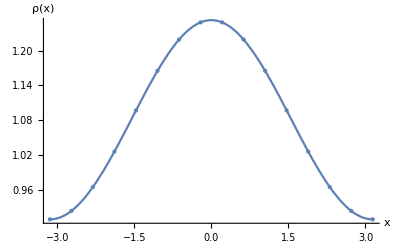

```mathematica
Show[ ListPlot[ GetRho[Soln1] , BaseStyle->14 , AxesLabel->{"x","ρ(x)"}, PlotStyle->PointSize[Large]], Plot[ InterpRho[x] , {x, -π, π}]   ]
```